```mathematica
(*Задание 1*)
```

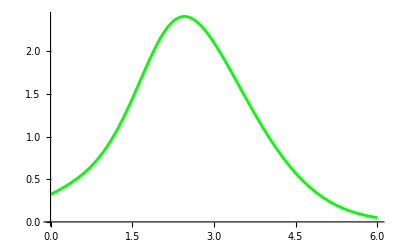

```mathematica
f[x_]= Exp[x-x^2/4]*Tanh[x^3/11+1/3];
a=0;b=6;n1=6;n2=10;x0=2.4316;h1=(b-a)/n1;h2=(b-a)/n2;
graphic = Plot[f[x],{x,a,b}, PlotStyle->{Green}]
```

```mathematica
table1 = N[Table[{a+i*h1,f[a+i*h1]},{i,0,n1}]]
```

{{0.,0.321513},{1.,0.847855},{2.,2.13629},{3.,2.10102},{4.,0.999991},{5.,0.286505},{6.,0.0497871}}

```mathematica
table2=N[Table[{a+i *h2,f[a+i *h2]},{i,0,n2}]]
```

{{0.,0.321513},{0.6,0.564545},{1.2,1.05291},{1.8,1.87865},{2.4,2.40318},{3.,2.10102},{3.6,1.43302},{4.2,0.810583},{4.8,0.382893},{5.4,0.151072},{6.,0.0497871}}

```mathematica
{TableForm[table1],TableForm[table2]}
```

{0. | 0.321513
1. | 0.847855
2. | 2.13629
3. | 2.10102
4. | 0.999991
5. | 0.286505
6. | 0.0497871,0. | 0.321513
0.6 | 0.564545
1.2 | 1.05291
1.8 | 1.87865
2.4 | 2.40318
3. | 2.10102
3.6 | 1.43302
4.2 | 0.810583
4.8 | 0.382893
5.4 | 0.151072
6. | 0.0497871}

```mathematica
(*Пункт а)*)
```

```mathematica
P1[x_]= ∏_(i=0)^n1 (x-table1[[i+1,1]])
```

(-6.+x) (-5.+x) (-4.+x) (-3.+x) (-2.+x) (-1.+x) (0.+x)

```mathematica
P2[x_]=∏_(i=0)^n2 (x-table2[[i+1,1]])
```

(-6.+x) (-5.4+x) (-4.8+x) (-4.2+x) (-3.6+x) (-3.+x) (-2.4+x) (-1.8+x) (-1.2+x) (-0.6+x) (0.+x)

```mathematica
Ln1[x_]  = Sum[table1[[i+1,2]]* P1[x]/((x-table1[[i+1,1]])*P1'[table1[[i+1,1]]]),{i,0,n1}]//Simplify
```

0.321513-1.13038 x+2.43962 x^2-0.827529 x^3+0.026763 x^4+0.0198283 x^5-0.00195986 x^6

```mathematica
Ln2 [x_] = Sum[table2[[i+1,2]]* P2[x]/((x-table2[[i+1,1]])*P2'[table2[[i+1,1]]]),{i,0,n2}]//Simplify
```

0.321513-3.94488 x+19.9019 x^2-36.6729 x^3+36.1106 x^4-20.7358 x^5+7.29855 x^6-1.60185 x^7+0.214312 x^8-0.0160188 x^9+0.000513301 x^10

```mathematica
(*n=6*)
```

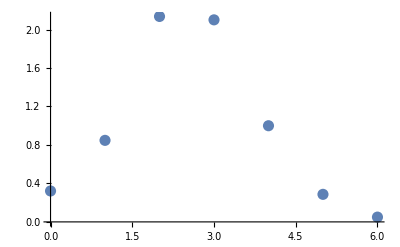

```mathematica
graphic1 = ListPlot[table1, PlotStyle->{PointSize[0.02]}]
```

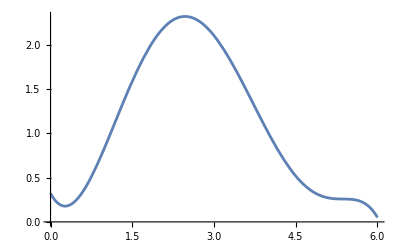

```mathematica
graphic1Ln = Plot[Ln1[x],{x,a,b}]
```

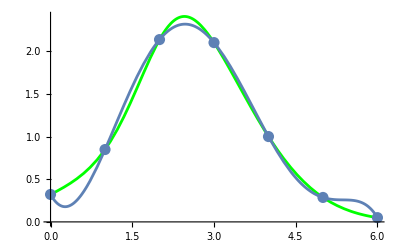

```mathematica
Show[graphic,graphic1,graphic1Ln]
```

```mathematica
(*n=10*)
```

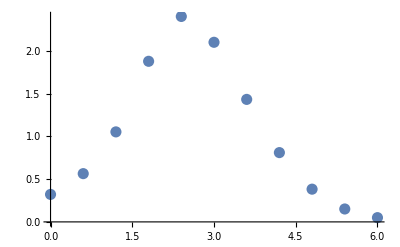

```mathematica
graphic2 = ListPlot[table2, PlotStyle->{PointSize[0.02]}]
```

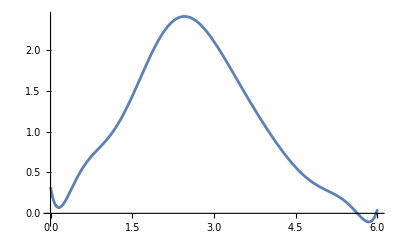

```mathematica
graphic2Ln = Plot[Ln2[x],{x,a,b}]
```

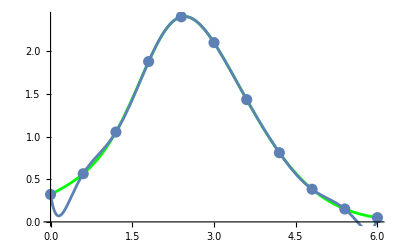

```mathematica
Show[graphic,graphic2,graphic2Ln]
```

```mathematica
(*Пункт б)*)
(*n=6*)
Array[difs1,{n1+1,n1+1},{0,0}];
For[j=1,j≤n1,j++,
For[i=n1,i≥n1-j,i--,
difs1[i,j]=""]];

For[i=0,i≤n1,i++,difs1[i,0]=table1[[i+1,2]]];

For[j=1,j≤n1,j++,
For[i=0,i≤n1-j,i++,
difs1[i,j]=difs1[i+1,j-1]-difs1[i,j-1]]];
difsTable1 = Array[difs1,{n1+1,n1+1},{0,0}];
PaddedForm[TableForm[difsTable1],{n1,n1-1}]
```

0.32151 |  0.52634 |  0.76209 | -2.08579 |  2.34372 | -1.14835 | -1.41110
 0.84786 |  1.28843 | -1.32370 |  0.25794 |  1.19537 | -2.55945 | 
 2.13629 | -0.03527 | -1.06576 |  1.45330 | -1.36408 |  | 
 2.10102 | -1.10103 |  0.38754 |  0.08923 |  |  | 
 0.99999 | -0.71349 |  0.47677 |  |  |  | 
 0.28650 | -0.23672 |  |  |  |  | 
 0.04979 |  |  |  |  |  |

```mathematica
(*n=10*)
Array[difs2,{n2+1,n2+1},{0,0}];
For[j=1,j≤n2,j++,
For[i=n2,i≥n2-j,i--,
difs2[i,j]=""]];

For[i=0,i≤n2,i++,difs2[i,0]=table2[[i+1,2]]];

For[j=1,j≤n2,j++,
For[i=0,i≤n2-j,i++,
difs2[i,j]=difs2[i+1,j-1]-difs2[i,j-1]]];
difsTable2 = Array[difs2,{n2+1,n2+1},{0,0}];
PaddedForm[TableForm[difsTable2],{n2,n2-1}]
```

0.321512738 |  0.243031949 |  0.245335116 |  0.092040878 | -0.730639709 |  0.843785730 |  0.029357340 | -1.938233386 |  4.670092421 | -7.898071573 |  11.262825750
 0.564544687 |  0.488367065 |  0.337375994 | -0.638598831 |  0.113146022 |  0.873143071 | -1.908876046 |  2.731859035 | -3.227979152 |  3.364754181 | 
 1.052911752 |  0.825743059 | -0.301222837 | -0.525452809 |  0.986289092 | -1.035732976 |  0.822982989 | -0.496120117 |  0.136775029 |  | 
 1.878654811 |  0.524520222 | -0.826675646 |  0.460836283 | -0.049443883 | -0.212749987 |  0.326862872 | -0.359345088 |  |  | 
 2.403175033 | -0.302155424 | -0.365839363 |  0.411392400 | -0.262193870 |  0.114112885 | -0.032482216 |  |  |  | 
 2.101019609 | -0.667994787 |  0.045553036 |  0.149198529 | -0.148080986 |  0.081630669 |  |  |  |  | 
 1.433024822 | -0.622441751 |  0.194751566 |  0.001117544 | -0.066450317 |  |  |  |  |  | 
 0.810583071 | -0.427690186 |  0.195869109 | -0.065332773 |  |  |  |  |  |  | 
 0.382892885 | -0.231821076 |  0.130536336 |  |  |  |  |  |  |  | 
 0.151071809 | -0.101284740 |  |  |  |  |  |  |  |  | 
 0.049787068 |  |  |  |  |  |  |  |  |  |

```mathematica
(*Пункт в)*)
```

```mathematica
q1 = (x-b)/h1;
Pn1 [x_] = difs1[n1,0];
P1[q_]=1;
For[k=1,k≤n1,k++,P1[q_]=P1[q1]*(q1+k-1);Pn1[x_]=Pn1[x]+P1[q1]/(k!) difs1[n1-k,k]];
Pn1[x]//Simplify
```

0.321513-1.13038 x+2.43962 x^2-0.827529 x^3+0.026763 x^4+0.0198283 x^5-0.00195986 x^6

```mathematica
q2 = (x-b)/h2;
Pn2 [x_] = difs2[n2,0];
P2[q_]=1;
For[k=1,k≤n2,k++,P2[q_]=P2[q2]*(q2+k-1);Pn2[x_]=Pn2[x]+P2[q2]/(k!) difs2[n2-k,k]];
Pn2[x]//Simplify
```

0.321513-3.94488 x+19.9019 x^2-36.6729 x^3+36.1106 x^4-20.7358 x^5+7.29855 x^6-1.60185 x^7+0.214312 x^8-0.0160188 x^9+0.000513301 x^10

```mathematica
graphic1Pn = Plot[Pn1[x],{x,a,b}]
```

-Graphics-

```mathematica
Show[graphic,graphic1,graphic1Pn]
```

-Graphics-

```mathematica
graphic2Pn = Plot[Pn2[x],{x,a,b}]
```

-Graphics-

```mathematica
Show[graphic,graphic2,graphic2Pn]
```

-Graphics-

```mathematica
(*Пункт г)*)
Npn1[x_] = InterpolatingPolynomial[table1,x]//Simplify
```

0.321513-1.13038 x+2.43962 x^2-0.827529 x^3+0.026763 x^4+0.0198283 x^5-0.00195986 x^6

```mathematica
Npn2[x_] = InterpolatingPolynomial[table2,x]//Simplify
```

0.321513-3.94488 x+19.9019 x^2-36.6729 x^3+36.1106 x^4-20.7358 x^5+7.29855 x^6-1.60185 x^7+0.214312 x^8-0.0160188 x^9+0.000513301 x^10

```mathematica
graphic1Npn = Plot[Npn1[x],{x,a,b}]
```

-Graphics-

```mathematica
Show[graphic,graphic1,graphic1Npn]
```

-Graphics-

```mathematica
graphic2Npn = Plot[Npn2[x],{x,a,b}]
```

-Graphics-

```mathematica
Show[graphic,graphic2,graphic2Npn]
```

-Graphics-

```mathematica
(*Пункт д)*)
Print["f[x0]=",f[x0]]
```

f[x0]=2.40655

```mathematica
Print["Ln1[x0]=",Ln1[x0],", Ln2[x0]=",Ln2[x0]]
```

Ln1[x0]=2.31605, Ln2[x0]=2.4066

```mathematica
Print["Pn1[x0]=",Pn1[x0],", Pn2[x0]=",Pn2[x0]]
```

Pn1[x0]=2.31605, Pn2[x0]=2.4066

```mathematica
Print["Npn1[x0]=",Npn1[x0],", Npn2[x0]=",Npn2[x0]]
```

Npn1[x0]=2.31605, Npn2[x0]=2.4066

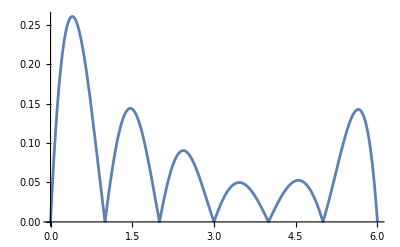

```mathematica
(*Пункт е)*)
Rn1[x_] = Abs[f[x]-Npn1[x]];
graphicError1 = Plot[Rn1[x],{x,a,b}]
```

```mathematica
maxError1 = FindMaximum[Rn1[x],{x,a,b}]
```

{0.260681,{x→0.398872}}

```mathematica
Rn2[x_] = Abs[f[x]-Npn2[x]];
```

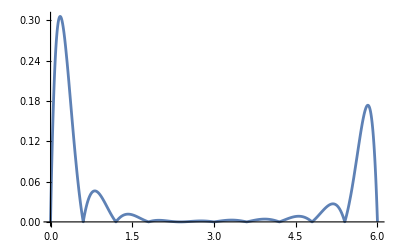

```mathematica
graphicError1 = Plot[Rn2[x],{x,a,b},PlotRange->Full]
```

```mathematica
maxError2 = FindMaximum[Rn2[x],{x,a,b}]
```

{0.305839,{x→0.176716}}

```mathematica
(*Пункт ж)*)
(*Исходя из полученных графиков, можно сказать, что при увелечении степени интерполяционного многочлена, погрешность интерполирования уменьшается*)
```

```mathematica
(*Задание 2*)
```

```mathematica
f[x_]= Exp[x-x^2/4]*Tanh[x^3/11+1/3];
a=0;b=6;n1=6;n2=10;x0=2.4316;
graphic = Plot[f[x],{x,a,b}, PlotStyle->{Green}]
```

-Graphics-

```mathematica
Clear[i];
T1[i_]=Cos[(Pi (2 i+1))/(2 n1+2)];
Clear[i];
T2[i_]=Cos[(Pi (2 i+1))/(2 n2+2)];
table1=Table[{x1=(a+b)/2+(b-a)/2*T1[i],f[x1]},{i,0,n1}]//N//Reverse;
table2=Table[{x2=(a+b)/2+(b-a)/2*T2[i],f[x2]},{i,0,n2}]//N//Reverse;
{TableForm[table1],TableForm[table2]}
```

{0.0752163 | 0.346176
0.654506 | 0.595002
1.69835 | 1.7323
3. | 2.10102
4.30165 | 0.722961
5.34549 | 0.165616
5.92478 | 0.0577876,0.0305357 | 0.331407
0.271104 | 0.416049
0.732751 | 0.642628
1.37808 | 1.27404
2.1548 | 2.28668
3. | 2.10102
3.8452 | 1.16042
4.62192 | 0.487425
5.26725 | 0.188487
5.7289 | 0.0840649
5.96946 | 0.0529101}

```mathematica
(*Пункт а)*)
```

```mathematica
difsTable1 = Array[difs1,{n1+1,n1+1},{0,0}];
For[j=1,j≤n1,j++,
For[i=n1,i≥n1-j,i--,
difs1[i,j]=""]];
For[i=0,i≤n1,i++,difs1[i,0]=table1[[i+1,2]]];
For[j=1,j≤n1,j++,For[i=0,i≤n1-j,i++,difs1[i,j]=(difs1[i+1,j-1]-difs1[i,j-1])/(table1[[i+1+j,1]]-table1[[i+1,1]])]];
PaddedForm[TableForm[difsTable1],{n1,n1-1}]
```

0.34618 |  0.42954 |  0.40662 | -0.25656 |  0.04956 |  0.00070 | -0.00343
 0.59500 |  1.08953 | -0.34375 | -0.04709 |  0.05325 | -0.01935 | 
 1.73230 |  0.28327 | -0.51549 |  0.20268 | -0.04872 |  | 
 2.10102 | -1.05870 |  0.22373 | -0.00323 |  |  | 
 0.72296 | -0.53394 |  0.21427 |  |  |  | 
 0.16562 | -0.18614 |  |  |  |  | 
 0.05779 |  |  |  |  |  |

```mathematica
difsTable2 = Array[difs2,{n2+1,n2+1},{0,0}];
For[j=1,j≤n2,j++,
For[i=n2,i≥n2-j,i--,
difs2[i,j]=""]];
For[i=0,i≤n2,i++,difs2[i,0]=table2[[i+1,2]]];
For[j=1,j≤n2,j++,For[i=0,i≤n2-j,i++,difs2[i,j]=(difs2[i+1,j-1]-difs2[i,j-1])/(table2[[i+1+j,1]]-table2[[i+1,1]])]];
PaddedForm[TableForm[difsTable2],{n2,n2-1}]
```

0.331406907 |  0.351841767 |  0.197894201 |  0.180043072 | -0.137676094 | -0.003337104 |  0.027764067 | -0.013567435 |  0.004087700 | -0.000945241 |  0.000182575
 0.416048897 |  0.490806162 |  0.440509780 | -0.112417663 | -0.147585507 |  0.102573426 | -0.034529273 |  0.007838680 | -0.001298623 |  0.000139057 | 
 0.642628218 |  0.978438829 |  0.228748817 | -0.515163160 |  0.219021525 | -0.047657172 |  0.004633905 |  0.000751065 | -0.000506224 |  | 
 1.274040499 |  1.303731325 | -0.939254200 |  0.166529596 |  0.033674625 | -0.026644743 |  0.008386336 | -0.001899885 |  |  | 
 2.286680928 | -0.219666151 | -0.528405682 |  0.275764856 | -0.069951341 |  0.009842683 | -0.000336769 |  |  |  | 
 2.101019609 | -1.112880654 |  0.151939343 |  0.058045056 | -0.034772669 |  0.008558024 |  |  |  |  | 
 1.160415473 | -0.866446823 |  0.283541921 | -0.036845942 | -0.009359924 |  |  |  |  |  | 
 0.487424753 | -0.463235735 |  0.214135282 | -0.056728916 |  |  |  |  |  |  | 
 0.188486564 | -0.226193645 |  0.137690693 |  |  |  |  |  |  |  | 
 0.084064887 | -0.129505092 |  |  |  |  |  |  |  |  | 
 0.052910062 |  |  |  |  |  |  |  |  |  |

```mathematica
(*Пункт б)*)
```

```mathematica
P1[x_]=1;
Pnr1[x_]=difs1[0,0];
P2[x_]=1;
Pnr2[x_]=difs2[0,0];
For[i=0,i<n1,i++,P1[x_]=P1[x] *(x-table1[[i+1,1]]);Pnr1[x_]=Pnr1[x]+difs1[0,i+1]*P1[x]]
Pnr1[x]//Simplify
```

0.347247-0.0619488 x+0.618925 x^2+0.22143 x^3-0.244875 x^4+0.0523616 x^5-0.00342699 x^6

```mathematica
For[i=0,i<n2,i++,P2[x_]=P2[x]*(x-table2[[i+1,1]]);Pnr2[x_]=Pnr2[x]+difs2[0,i+1]*P2[x]]
Pnr2[x]//Simplify
```

0.338436-0.355155 x+4.39344 x^2-10.2318 x^3+12.0162 x^4-7.56577 x^5+2.76514 x^6-0.610448 x^7+0.0806188 x^8-0.00588033 x^9+0.000182575 x^10

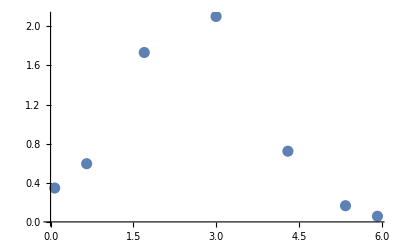

```mathematica
graphic1 = ListPlot[table1, PlotStyle->{PointSize[0.02]}]
```

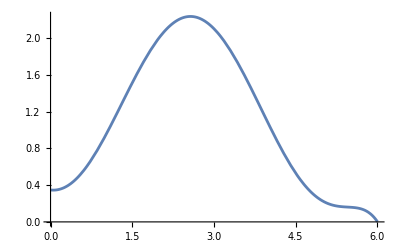

```mathematica
graphic1Pnr = Plot[Pnr1[x],{x,a,b}]
```

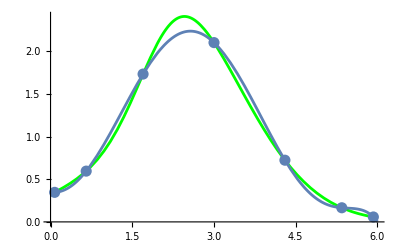

```mathematica
Show[graphic,graphic1,graphic1Pnr]
```

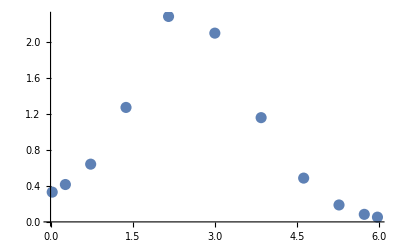

```mathematica
graphic2 = ListPlot[table2, PlotStyle->{PointSize[0.02]}]
```

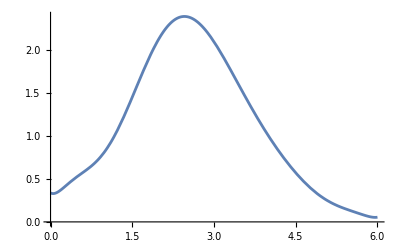

```mathematica
graphic2Pnr = Plot[Pnr2[x],{x,a,b}]
```

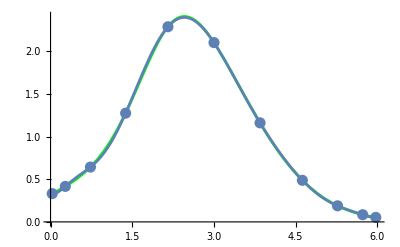

```mathematica
Show[graphic,graphic2,graphic2Pnr]
```

```mathematica
(*Пункт в)*)
Intf1=Interpolation[table1]
```

InterpolatingFunction[…]

```mathematica
graphic1Intf=Plot[Intf1[x],{x,0.07521626345452903,5.924783736545471}];
```

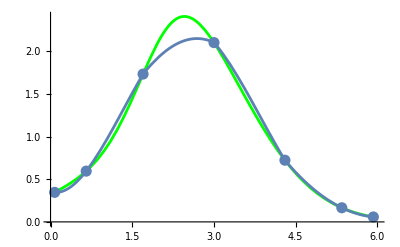

```mathematica
Show[graphic,graphic1,graphic1Intf]
```

```mathematica
Intf2=Interpolation[table2]
```

InterpolatingFunction[…]

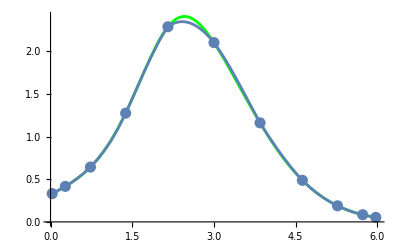

```mathematica
graphic2Intf=Plot[Intf2[x],{x,0.03053567435720206,5.969464325642798}];
Show[graphic,graphic2,graphic2Intf]
```

```mathematica
(*Пункт г)*)
```

```mathematica
Print["f[x]=",f[x0]]
```

f[x]=2.40655

```mathematica
Print["Pnr1[x0]=",Pnr1[x0],", Pnr2[x0]=",Pnr2[x0]]
```

Pnr1[x0]=2.22167, Pnr2[x0]=2.39573

```mathematica
Print["Intf1[x0]=",Intf1[x0],", Intf2[x0]=",Intf2[x0]]
```

Intf1[x0]=2.11815, Intf2[x0]=2.34605

```mathematica
(*Пункт д)*)
```

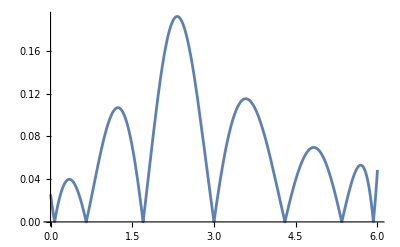

```mathematica
Rnp1[x_]=Abs[f[x]-Pnr1[x]];
graphicErrorp1=Plot[Rnp1[x],{x,a,b},PlotRange->Full]
```

```mathematica
maxErrorp1=FindMaximum[Rnp1[x],{x,2,3}]
```

{0.192101,{x→2.32455}}

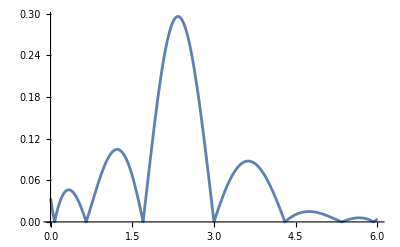

```mathematica
RnInt1[x_]=Abs[f[x]-Intf1[x]];
graphErrorInt1=Plot[RnInt1[x],{x,a,b},PlotRange->Full]
```

```mathematica
maxErrI1=FindMaximum[RnInt1[x],{x,2,3}]
```

{0.296223,{x→2.33885}}

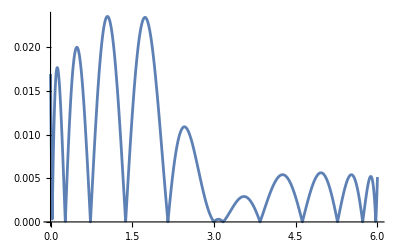

```mathematica
Rnp2[x_]=Abs[f[x]-Pnr2[x]];
graphicErrorp2=Plot[Rnp2[x],{x,a,b},PlotRange->Full]
```

```mathematica
maxErrorp2=FindMaximum[Rnp2[x],{x,1.5,2.5}]
```

{0.0234122,{x→1.734}}

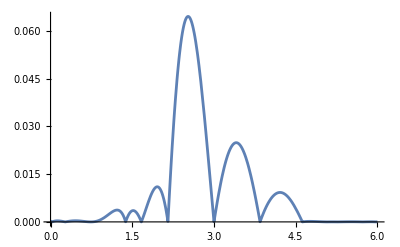

```mathematica
RnInt2[x_]=Abs[f[x]-Intf2[x]];
graphErrorInt2=Plot[RnInt2[x],{x,a,b},PlotRange->Full]
```

```mathematica
maxErrorInt2=FindMaximum[RnInt2[x],{x,2.5,3}]
```

{0.0645414,{x→2.52475}}

```mathematica
(*Задание 3*)
(*Из сравнения результатов вычисления максимальных погрешностей, сделаем вывод о том, что с увелечением количества узлов интерполяциии возрастает точность построения интерполяционных многочленов
(в 1 и 2 задании погрешности при n=6 больше чем при n=10), также из сравнения понятно, что в качестве узлов интерполяции нужно брать точки, вычесленные с использованием корней многочлена Чебышева(т.к. в 1 задании погрешности больше чем во 2)*)
(*Задание 4*)
```

```mathematica
f[x_]= Exp[x-x^2/4]*Tanh[x^3/11+1/3];
a=0;b=6;n=10;x0=2.4316;h=(b-a)/n;
```

```mathematica
graphic=Plot[f[x],{x,a,b},PlotStyle->{Green}]
```

-Graphics-

```mathematica
table=Table[{a+i* h,f[a+i* h]},{i,0,n}]//N;
```

```mathematica
TableForm[table]
```

0. | 0.321513
0.6 | 0.564545
1.2 | 1.05291
1.8 | 1.87865
2.4 | 2.40318
3. | 2.10102
3.6 | 1.43302
4.2 | 0.810583
4.8 | 0.382893
5.4 | 0.151072
6. | 0.0497871

```mathematica
listC=Table[0,{i,0,n}];
A=Table[0,{n-1},{n-1}];
Do[If[i≠1,A[[i,i-1]]=h];A[[i,i]]=3 h;If[i≠n-1,A[[i,i+1]]=h],{i,1,n-1}]
MatrixForm[A]//N
```

(1.8 | 0.6 | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0.6 | 1.8 | 0.6 | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0.6 | 1.8 | 0.6 | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0.6 | 1.8 | 0.6 | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0.6 | 1.8 | 0.6 | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0.6 | 1.8 | 0.6 | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0.6 | 1.8 | 0.6 | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0.6 | 1.8 | 0.6
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.6 | 1.8)

```mathematica
B=Table[3 ((table[[i,2]]-table[[i-1,2]])/h-(table[[i-1,2]]-table[[i-2,2]])/h),{i,3,n+1}]//N;
```

```mathematica
X=LinearSolve[A,B];
```

```mathematica
For[i=1,i≤n-1,i++,listC[[i+1]]=X[[i]]];
```

```mathematica
MatrixForm[listC]
```

(0
0.352869
0.985851
-0.498957
-1.99917
-0.392495
0.127994
0.388122
0.33057
0.252411
0)

```mathematica
listA=Table[table[[i+1,2]],{i,1,n}]
```

{0.564545,1.05291,1.87865,2.40318,2.10102,1.43302,0.810583,0.382893,0.151072,0.0497871}

```mathematica
listB = Table[(table[[i,2]]-table[[i-1,2]])/h+2/3 h listC[[i]]+1/3 h listC[[i-1]],{i,2,n+1}]
```

{0.546201,1.27886,1.37383,-0.0252593,-1.06042,-1.14063,-0.856555,-0.502965,-0.21929,-0.118326}

```mathematica
listD=Table[(listC[[i]]-listC[[i-1]])/(3 h),{i,2,n+1}]
```

{0.196038,0.351657,-0.824894,-0.833452,0.892598,0.28916,0.144516,-0.0319734,-0.0434216,-0.140228}

```mathematica
sTable=Table[{listA[[i]]+listB[[i]] (x-table[[i+1,1]])+listC[[i+1]] ((x-table[[i+1,1]])^2)+listD[[i]] ((x-table[[i+1,1]])^3),table[[i,1]]≤x≤table[[i+1,1]]}, {i,1,n}]//Simplify
```

{{0.321513+0.334479 x+0.196038 x^3,0.≤x≤0.6},{0.330244+0.431973 x-0.280113 x^2+0.351657 x^3,0.6≤x≤1.2},{2.59993-4.84789 x+3.95547 x^2-0.824894 x^3,1.2≤x≤1.8},{2.47021-4.83129 x+4.00168 x^2-0.833452 x^3,1.8≤x≤2.4},{-22.3503+25.3947 x-8.42587 x^2+0.892598 x^3,2.4≤x≤3.},{-6.29299+9.18037 x-2.99494 x^2+0.28916 x^3,3.≤x≤3.6},{0.547712+3.53099 x-1.43278 x^2+0.144516 x^3,3.6≤x≤4.2},{13.9495-5.88644 x+0.790987 x^2-0.0319734 x^3,4.2≤x≤4.8},{15.5329-6.74385 x+0.955841 x^2-0.0434216 x^3,4.8≤x≤5.4},{31.0491-15.263 x+2.52411 x^2-0.140228 x^3,5.4≤x≤6.}}

```mathematica
S[x_]=Piecewise[sTable]
```

Piecewise[{{0.321513+0.334479 x+0.196038 x^3, 0.≤x≤0.6}, {0.330244+0.431973 x-0.280113 x^2+0.351657 x^3, 0.6≤x≤1.2}, {2.59993-4.84789 x+3.95547 x^2-0.824894 x^3, 1.2≤x≤1.8}, {2.47021-4.83129 x+4.00168 x^2-0.833452 x^3, 1.8≤x≤2.4}, {-22.3503+25.3947 x-8.42587 x^2+0.892598 x^3, 2.4≤x≤3.}, {-6.29299+9.18037 x-2.99494 x^2+0.28916 x^3, 3.≤x≤3.6}, {0.547712+3.53099 x-1.43278 x^2+0.144516 x^3, 3.6≤x≤4.2}, {13.9495-5.88644 x+0.790987 x^2-0.0319734 x^3, 4.2≤x≤4.8}, {15.5329-6.74385 x+0.955841 x^2-0.0434216 x^3, 4.8≤x≤5.4}, {31.0491-15.263 x+2.52411 x^2-0.140228 x^3, 5.4≤x≤6.}, {0, True}}]

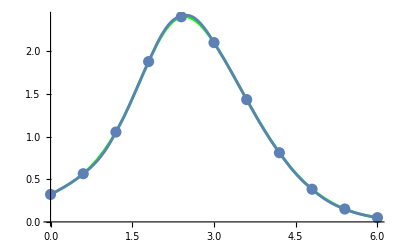

```mathematica
graphic1=ListPlot[table,PlotStyle->{PointSize[0.02]}];
graphicS = Plot[S[x],{x,a,b}];
Show[graphic,graphic1,graphicS]
```

```mathematica
(*Пункт б)*)
Sf[x_] = Interpolation[table,x,Method->"Spline"]
```

InterpolatingFunction[…][x]

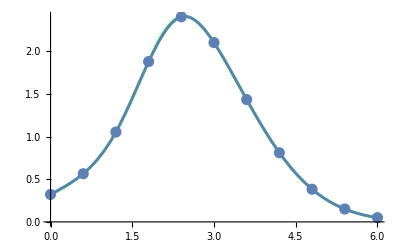

```mathematica
graphicSf = Plot[Sf[x],{x,a,b}];
Show[graphic,graphic1,graphicSf]
```

```mathematica
(*Пункт в)*)
Needs["Splines`"]
Spl=SplineFit[table,Cubic]
```

SplineFunction[Cubic, {0.,10.}, <>]

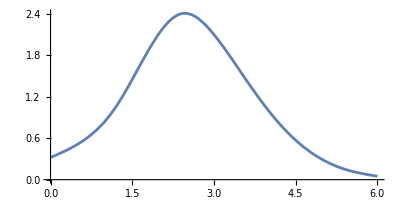

```mathematica
t = (x-a)/h;
graphicSpl= ParametricPlot[Spl[t],{t,0,n},AspectRatio->1/2]
```

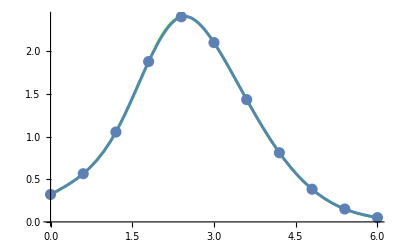

```mathematica
Show[graphic,graphic1,graphicSpl]
```

```mathematica
(*Пункт г)*)
```

```mathematica
Print["f[x0]=",f[x0]]
```

f[x0]=2.40655

```mathematica
Print["S[x0]=",S[x0]]
```

S[x0]=2.41304

```mathematica
Print["Sf[x0]=",Sf[x0]]
```

Sf[x0]=2.40749

```mathematica
Print["Spl[x0]=",Last[Spl[(x0-a)/h]]]
```

Spl[x0]=2.40749

```mathematica
(*Задание 5*)
f[x_]= Exp[x-x^2/4]*Tanh[x^3/11+1/3];
a=0;b=6;n=10;x0=2.4316;h=(b-a)/n;
table=Table[{a+i* h,f[a+i* h]},{i,0,n}]//N;
TableForm[table]
```

0. | 0.321513
0.6 | 0.564545
1.2 | 1.05291
1.8 | 1.87865
2.4 | 2.40318
3. | 2.10102
3.6 | 1.43302
4.2 | 0.810583
4.8 | 0.382893
5.4 | 0.151072
6. | 0.0497871

```mathematica
(*Пункт а)*)
m = 1;
A1  = Table[If[i+j!=0,∑_(k=0)^n (table[[k+1,1]])^(i+j),n+1], {i, 0, m}, {j, 0, m}]
```

{{11,33.},{33.,138.6}}

```mathematica
B1 = Table[If[i!=0,∑_(k=0)^n (table[[k+1,2]]*(table[[k+1,1]])^i), ∑_(l=0)^n table[[l+1,2]]], {i, 0, m}]
```

{11.1492,28.5702}

```mathematica
Ai1 = LinearSolve[A1,B1]
```

{1.38306,-0.123165}

```mathematica
Q1[x_]=∑_(i=0)^m (Ai1[[i+1]]*x^i)
```

1.38306-0.123165 x

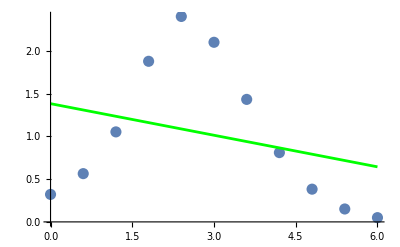

```mathematica
graphic1 = ListPlot[table,PlotStyle->{PointSize[0.02]}];
graphicQ1 = Plot[Q1[x],{x,a,b},PlotStyle->Green];
Show[graphic1,graphicQ1]
```

```mathematica
(*Пункт б)*)
m = 2;
A2  = Table[If[i+j!=0,∑_(k=0)^n (table[[k+1,1]])^(i+j),n+1], {i, 0, m}, {j, 0, m}]
```

{{11,33.,138.6},{33.,138.6,653.4},{138.6,653.4,3283.16}}

```mathematica
B2 = Table[If[i!=0,∑_(k=0)^n (table[[k+1,2]]*(table[[k+1,1]])^i), ∑_(l=0)^n table[[l+1,2]]], {i, 0, m}]
```

{11.1492,28.5702,88.4479}

```mathematica
Ai2 = LinearSolve[A2,B2]
```

{0.277391,1.10535,-0.204753}

```mathematica
Q2[x_]=∑_(i=0)^m (Ai2[[i+1]]*x^i)
```

0.277391+1.10535 x-0.204753 x^2

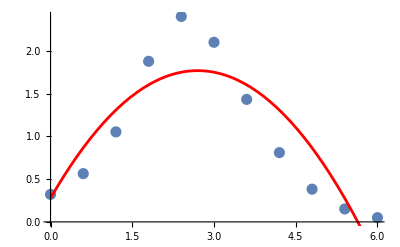

```mathematica
graphicQ2 =Plot[Q2[x],{x,a,b},PlotStyle->Red];
Show[graphic1,graphicQ2]
```

```mathematica
(*Пункт в)*)
Q3[x_]=Fit[table,{1,x,x^2,x^3},x]
```

-0.0527996+1.97975 x-0.586918 x^2+0.0424628 x^3

```mathematica
Q4[x_]=Fit[table,{1,x,x^2,x^3,x^4},x]
```

0.253095+0.209525 x+0.888266 x^2-0.35092 x^3+0.0327819 x^4

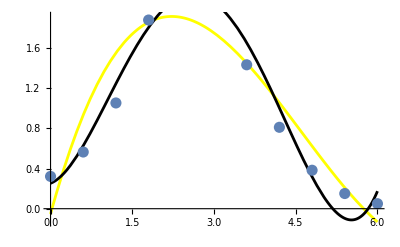

```mathematica
graphicQ3 = Plot[Q3[x],{x,a,b},PlotStyle->{Yellow}];
graphicQ4 = Plot[Q4[x],{x,a,b},PlotStyle->{Black}];
Show[graphicQ3,graphicQ4,graphic1]
```

```mathematica
(*Пункт г)*)
Print["Q1[x0]=",Q1[x0],", Q2[x0]=",Q2[x0],", Q3[x0]=",Q3[x0],", Q4[x0]=",Q4[x0]]
```

Q1[x0]=1.08357, Q2[x0]=1.75453, Q3[x0]=1.90139, Q4[x0]=2.11539

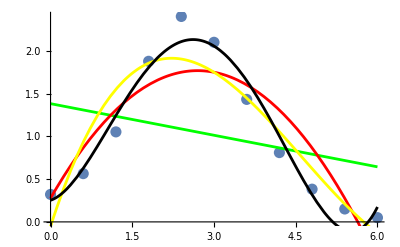

```mathematica
(*Пункт д)*)
Show[graphic1,graphicQ1,graphicQ2,graphicQ3,graphicQ4]
```